# When should genomic imprinting affect sexual maturation? Shared trait across both sexes

```mathematica
Clear["Global`*"]
```

## Parameters

```mathematica
tdip={tff->1/2,tmf->1/2,tfm->1/2,tmm->1/2};
thapdip={tff->1/2,tmf->1,tfm->1/2,tmm->0};
```

Fecundity and survival functions:

```mathematica
ϕ[a_]:=(k a)^3
σ[a_]:=Exp[-μ a]
```

## Fitness expressions

w_ij: expected number of mutant offspring of sex i contributed by a sex j focal parent

```mathematica
wff=tff f[afocfF](((1-df)s[ajfocfF])/(f[aalocfF](1-df)s[ajlocfF]+f[a]df s[a])+(df s[ajfocfF])/(f[a]s[a]));
```

```mathematica
wmf=tmf f[afocfF]((nm(1-dm)s[ajfocmF])/(nf(f[aalocfF](1-dm)s[ajlocmF]+dm f[a]s[a]))+(nm dm s[ajfocmF])/(nf f[a]s[a]));
wfm=tfm nf/nm(l g[afocmM]/(l g[aalocmM]+(1-l)g[a])f[aalocfM](((1-df)s[ajfocfM])/(f[aalocfM](1-df)s[ajlocfM]+df f[a] s[a])+(df s[ajfocfM])/(f[a]s[a]))+(1-l)g[afocmM]/g[a] s[ajfocnonlocfM]/s[a]);
wmm=tmm nf/nm(l  g[afocmM]/(l g[aalocmM]+(1-l)g[a])f[aalocfM]((nm (1-dm)s[ajfocmM])/(nf(f[aalocfM](1-dm)s[ajlocmM]+dm f[a]s[a]))+dm nm/nf s[ajfocmM]/(f[a]s[a]))+(1-l)nm/nf g[afocmM]/g[a] s[ajfocnonlocmM]/s[a]);
```

## Reproductive values, class frequencies

Demographical model of homogeneous population

```mathematica
subsMutant={aalocfF->a,aalocfM->a,afocfF->a,aalocmM->a,afocmM->a,ajfocfF->a,ajfocfM->a,ajfocmF->a,ajfocmM->a,ajfocnonlocfM->a,ajfocnonlocmM->a,ajlocfF->a,ajlocfM->a,ajlocmF->a,ajlocmM->a};
```

```mathematica
A={{wff,wfm},{wmf,wmm}}/.subsMutant//Simplify;
```

```mathematica
A//Variables
```

{nf,nm,tff,tfm,tmf,tmm}

```mathematica
evals=Simplify[Eigenvalues[A]]
```

{1/2 (tff+tmm-√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)),1/2 (tff+tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2))}

```mathematica
classfreqs=Simplify[Eigenvectors[1/evals[[1]] A]]
```

{{(nf (tff-tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nm tmf),1},{-(nf (-tff+tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nm tmf),1}}

```mathematica
repvals=Simplify[Eigenvectors[1/evals[[1]] Transpose[A]]]
```

{{(nm (tff-tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nf tfm),1},{-(nm (-tff+tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nf tfm),1}}

### Diplodiploidy

Stable class frequencies

```mathematica
udipR=Simplify[classfreqs[[1]]/Total[classfreqs[[1]]]/.tdip]
```

{nf/(nf+nm),nm/(nf+nm)}

```mathematica
udip={uf->udipR[[1]],um->udipR[[2]]};
```

Individual reproductive values

```mathematica
vdipR=Simplify[repvals[[1]]/(udipR.repvals[[1]])/.tdip]
```

{(nf+nm)/(2 nf),(nf+nm)/(2 nm)}

```mathematica
vdip={vf->vdipR[[1]],vm->vdipR[[2]]};
```

Class reproductive values

```mathematica
cdip={cf->vf uf,cm->vm um}/.vdip/.udip
```

{cf→1/2,cm→1/2}

### Haplodiploidy

```mathematica
uhapdipR=Simplify[classfreqs[[1]]/Total[classfreqs[[1]]]/.thapdip]
```

{nf/(nf+nm),nm/(nf+nm)}

```mathematica
uhapdip={uf->uhapdipR[[1]],um->uhapdipR[[2]]};
```

Individual reproductive values

```mathematica
vhapdipR=Simplify[repvals[[1]]/(uhapdipR.repvals[[1]])/.thapdip]
```

{(2 (nf+nm))/(3 nf),(nf+nm)/(3 nm)}

```mathematica
vhapdip={vf->vhapdipR[[1]],vm->vhapdipR[[2]]};
```

Class reproductive values

```mathematica
chapdip={cf->vf uf,cm->vm um}/.vhapdip/.uhapdip
```

{cf→2/3,cm→1/3}

## Selection gradient on a

```mathematica
Wfaf=wff+vm/vf wmf;
Wmaf=wmm+vf/vm wfm;
```

```mathematica
selgrada=cf(
D[Wfaf,afocfF]rfi
+D[Wfaf,ajfocfF]rfownjf
+D[Wfaf,ajfocmF]rfownjm
+D[Wfaf,aalocfF]rff
+D[Wfaf,ajlocfF]rflocjf
+D[Wfaf,ajlocmF]rflocjm
)+cm(
D[Wmaf,afocmM]rmi
+D[Wmaf,aalocmM]rmm
+D[Wmaf,aalocfM]rmf
+D[Wmaf,ajfocfM]rmownjf
+D[Wmaf,ajfocmM]rmownjm
+D[Wmaf,ajlocfM]rmlocjf
+D[Wmaf,ajlocmM]rmlocjm
+D[Wmaf,ajfocnonlocfM]rmownjfnonloc
+D[Wmaf,ajfocnonlocmM]rmownjmnonloc
)/.subsMutant;
```

## Relatedness

### Diplodiploidy

#### Coefficients of consanguinity

```mathematica
hf=1-df;
hm=1-dm;
```

```mathematica
Qdip={QffJ==QmmJ==QfmJ==1/4(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm+1/4 l^2(1/nm Qm+(nm-1)/nm Qmm),
Qf==1/2(1+l Qfm),
Qf==Qm,
Qff==hf^2 QffJ,
Qmm==hm^2 QmmJ,
Qfm==hf hm QfmJ,
Qmf==Qfm};
```

```mathematica
Qsoldip=Solve[Qdip,{QffJ,QmmJ,QfmJ,Qff,Qf,Qm,Qmm,Qfm,Qmf}]//Simplify//Flatten;
```

#### Relatedness coefficients

```mathematica
rdip={
rfi->Qf,
rmi->Qm,
rfownjm->Qf,
rfownjf->Qm,
rmownjf->1/2+1/2 Qfm,
rmownjm->1/2+1/2 Qfm,
rmownjfnonloc->1/2,
rmownjmnonloc->1/2,
rff->1/nf Qf+(nf-1)/nf Qff,
rmf->Qmf,
rmm->l 1/nm Qm+l(nm-1)/nm Qmm,
rflocjf->1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf(Qff+l Qfm),
rflocjm->1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf(Qff+l Qfm),
rmlocjf->1/2 1/nm l(Qm+Qfm)+1/2 l(nm-1)/nm(Qfm+Qmm)+1/2(1-l)Qfm,
rmlocjm->1/2 1/nm l(Qm+Qfm)+1/2 l(nm-1)/nm(Qfm+ Qmm)+1/2(1-l)Qfm
}/.Qsoldip;
```

```mathematica
rdipM={
rfi->1/2(Qf+l Qfm),
rmi->1/2(Qf+l Qfm),
rfownjm->Qf,
rfownjf->Qf,
rmownjf->Qfm,
rmownjm->Qfm,
rmownjfnonloc->0,
rmownjmnonloc->0,
rff->1/2 1/nf(Qf+l Qfm)+(nf-1)/nf hf^2(1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf(Qff+l Qfm)),
rmf->1/2 hm hf(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rmm->1/2 1/nm l(Qf+l Qfm)+ hm^2(nm-1)/nm l(1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf(Qff+l Qfm)),
rflocjf->1/nf Qf+(nf-1)/nf Qff,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->Qfm,
rmlocjm->Qfm
}/.Qsoldip;
```

Expression by father (P)

```mathematica
rdipP={
rfi->1/2(Qm+l Qfm),
rmi-> 1/2(Qm+l Qfm),
rfownjf->l Qfm,
rfownjm->l Qfm,
rmownjm->Qm,
rmownjf->Qm,
rmownjfnonloc->Qm,
rmownjmnonloc->Qm,
rff->1/2 1/nf(Qm+l Qfm)+1/2(nf-1)/nf hf^2(1/nm l(Qm+Qfm)+(nm-1)/nm l(l Qmm+Qfm)),
rmf->1/2 hf hm (1/nm l(Qm+Qfm)+(nm-1)/nm l(l Qmm+Qfm)),
rmm->1/2 1/nm l(Qm+l Qfm)+1/2(nm-1)/nm hm^2 l(1/nm l(Qm+Qfm)+(nm-1)/nm l(l Qmm+Qfm)),
rflocjf->l Qfm,
rflocjm->l Qfm,
rmlocjf->l 1/nm Qm+l (nm-1)/nm Qmm,
rmlocjm->l 1/nm Qm+l (nm-1)/nm Qmm
}/.Qsoldip;
```

Expression by maternally-inherited alleles (MI)

```mathematica
rdipMI={
rfi->Qf,
rmi->Qm,
rfownjf->1,
rfownjm->1,
rmownjf->Qfm,
rmownjm->Qfm,
rmownjfnonloc->0,
rmownjmnonloc->0,
rff->1/nf Qf+1/2(nf-1)/nf hf^2(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rfm->1/2 hm hf 1/nf(Qf+l Qfm)+1/2 hm hf(nf-1)/nf(Qff+l Qfm),
rmf->1/2 hm hf 1/nf(Qf+l Qfm)+1/2 hm hf(nf-1)/nf(Qff+l Qfm),
rmm->l 1/nm Qf+1/2(nm-1)/nm hm^2 l(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rflocjf->1/nf Qf+(nf-1)/nf Qff,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->Qmf,
rmlocjm->Qmf}/.Qsoldip;
```

```mathematica
rdipPI={
rfi->Qf,
rmi->Qm,
rfownjf->l Qfm,
rfownjm->l Qfm,
rmownjf->1,
rmownjm->1,
rmownjfnonloc->1,
rmownjmnonloc->1,
rff->1/nf Qm+1/2(nf-1)/nf hf^2(1/nm l(Qm+Qfm)+(nm-1)/nm l(l Qmm+Qfm)),
rfm->1/2 hf hm (l 1/nm(Qm+Qfm)+(nm-1)/nm l (l Qmm+Qfm)),
rmf->1/2 hf hm (l 1/nm(Qm+Qfm)+(nm-1)/nm l (l Qmm+Qfm)),
rmm->l 1/nm Qm+1/2(nm-1)/nm hm^2 l(1/nm l(Qm+Qfm)+(nm-1)/nm l(l Qmm+Qfm)),
rflocjf->l Qfm,
rflocjm->l Qfm,
rmlocjf->l(1/nm Qm+(nm-1)/nm Qmm),
rmlocjm->l(1/nm Qm+(nm-1)/nm Qmm)}/.Qsoldip;
```

### Haplodiploidy

#### Coefficients of consanguinity haplodiploidy

```mathematica
Qhapdip={QffJ==1/4(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm+1/4 l^2(1/nm Qm+(nm-1)/nm Qmm),
QfmJ==QmfJ==1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
QmmJ==1/nf Qf+(nf-1)/nf Qff,
Qf==1/2(1+l Qfm),
Qm==1,
Qff==hf^2 QffJ,
Qmm==hm^2 QmmJ,
Qfm==hf hm QfmJ,
Qmf==Qfm};
```

```mathematica
Qsolhapdip=Solve[Qhapdip,{QffJ,QmmJ,QfmJ,QmfJ,Qff,Qf,Qm,Qmm,Qfm,Qmf}]//Simplify//Flatten;
```

#### Relatedness coefficients haplodiploidy

Expression of alleles in offspring

```mathematica
rhapdip={
rfi->Qf,
rmi->Qm,
rfownjf->Qf,
rfownjm->Qm,
rmownjf->1/2 Qm+1/2 Qfm,
rmownjm->Qfm,
rmownjfnonloc->1/2,
rmownjmnonloc->0,
rff->1/nf Qf+(nf-1)/nf Qff,
rfm->Qmf,
rmf->Qmf,
rmm->l 1/nm Qm+l(nm-1)/nm Qmm,
rflocjf->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->1/2 1/nm l(Qm+Qfm)+1/2 l (nm-1)/nm(Qfm+Qmm)+1/2(1-l)Qfm,
rmlocjm->Qmf
}/.Qsolhapdip;
```

Expression controlled by mother (M)

```mathematica
rhapdipM={
rfi->1/2(Qf+l Qfm),
rmi->Qf,
rfownjf->Qf,
rfownjm->Qf,
rmownjf->Qfm,
rmownjm->Qfm,
rmownjfnonloc->0,
rmownjmnonloc->0,
rff->1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf hf^2(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rfm->1/2 hf hm(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rmf->hf hm(1/nf Qf+(nf-1)/nf Qff),
rmm->l 1/nm Qf+(nm-1)/nm hm^2 l(1/nf Qf+(nf-1)/nf Qff),
rflocjf->1/nf Qf+(nf-1)/nf Qff,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->Qmf,
rmlocjm->Qmf
}/.Qsolhapdip;
```

Expression controlled by father (P)

```mathematica
rhapdipP={
rfi->1/2(Qm+l Qfm),
rmi->Qm,
rfownjf->l Qfm,
rfownjm->Qm,
rmownjf->Qm,
rmownjm->Qfm,
rmownjfnonloc->Qm,
rmownjmnonloc->0,
rff->1/2 1/nf(Qm+l Qfm)+1/2(nf-1)/nf hf^2(1/nm l(Qm+Qfm)+(nm-1)/nm l (l Qmm+Qfm)),
rfm->Qmf,
rmf->hm hf Qmf,
rmm->l 1/nm Qm+l(nm-1)/nm Qmm,
rflocjf->l Qfm,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->l(1/nm Qm+(nm-1)/nm Qmm),
rmlocjm->Qmf
}/.Qsolhapdip;
```

```mathematica
rhapdipMI={
rfi->Qf,
rmi->Qm,
rfownjf->1,
rfownjm->1,
rmownjf->Qfm,
rmownjm->Qfm,
rmownjfnonloc->0,
rmownjmnonloc->0,
rff->1/nf Qf+1/2(nf-1)/nf hf^2(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rfm->1/2 hf hm(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rmf->hf hm(1/nf Qf+(nf-1)/nf Qff),
rmm->l 1/nm Qm+(nm-1)/nm hm^2 l(1/nf Qf+(nf-1)/nf Qff),
rflocjf->1/nf Qf+(nf-1)/nf Qff,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->Qmf,
rmlocjm->Qmf}/.Qsolhapdip;
```

```mathematica
rhapdipPI={
rfi->Qf,
rmi->Qm,
rfownjf->l Qfm,
rfownjm->Qm,
rmownjf->1,
rmownjm->Qfm,
rmownjfnonloc->Qm,
rmownjmnonloc->0,
rff->1/nf Qf+(nf-1)/nf hf^2(l 1/nm Qf+(nm-1)/nm l(l Qmm+Qmf)),
rmf->l Qmf,
rfm->Qmf,
rmm->l 1/nm Qm+l(nm-1)/nm Qmm,
rflocjf->l Qfm,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->l(1/nm Qm+(nm-1)/nm Qmm),
rmlocjm->Qmf}/.Qsolhapdip;
```

## Analytical results diplodiploidy

```mathematica
asol=Solve[selgrada==0,s'[a]]//FullSimplify//Flatten
```

{s'[a]→(s[a] (-(cf nm vm (nf ((-1+df)^2 rff-rfi) tff vf+nm ((-1+dm)^2 rff-rfi) tmf vm)+cm l nf rmf vf ((-2+df) df nf tfm vf+(-2+dm) dm nm tmm vm)) g[a] f'[a]+cm nf (rmi-l^2 rmm) vf (nf tfm vf+nm tmm vm) f[a] g'[a]))/((cf nm vm (nf ((-1+df)^2 rflocjf-rfownjf) tff vf+nm ((-1+dm)^2 rflocjm-rfownjm) tmf vm)+cm nf vf (nf (-rmownjfnonloc+l ((-1+df)^2 rmlocjf-rmownjf+rmownjfnonloc)) tfm vf+nm (-rmownjmnonloc+l ((-1+dm)^2 rmlocjm-rmownjm+rmownjmnonloc)) tmm vm)) f[a] g[a])}

```mathematica
asol[[1]]/.{l->0,df->1,dm->1,rmi->1,rfi->1,rfownjf->1/2,rfownjm->1/2,rmownjmnonloc->1/2,rmownjfnonloc->1/2,tff->1/2,tfm->1/2}//FullSimplify
```

s'[a]→-(2 s[a] (cf nm vm (nf vf+2 nm tmf vm) g[a] f'[a]+cm nf vf (nf vf+2 nm tmm vm) f[a] g'[a]))/((cf nm vm (nf vf+2 nm tmf vm)+cm nf vf (nf vf+2 nm tmm vm)) f[a] g[a])

```mathematica
asol[[1]]/.rdip/.vdip/.cdip/.{df->1,dm->1,l->0}/.tdip//Simplify
```

s'[a]→-(s[a] (g[a] f'[a]+f[a] g'[a]))/(2 f[a] g[a])

```mathematica
asol[[1]]/.rhapdip/.vhapdip/.chapdip/.{df->1,dm->1,l->0}/.thapdip//Simplify
```

s'[a]→-(s[a] (g[a] f'[a]+f[a] g'[a]))/(2 f[a] g[a])

```mathematica
rfcoeff={rfselfjuvf->rfkidf+l rmkidf+(1-l)rmkidfnonloc,
rfcompetingjuvf->hf^2(rflocjf+l rmlocjf),
rfownoffspring->rfocfF+l rmf,
rfcompetingoffspring->1/2(hf^2+hm^2)(rff+l rmf)
};
rmcoeff={rmselfjuvm->l rmkidm+rfkidm+(1-l)rmkidmnonloc,
rmcompetingjuvm->hm^2(rflocjm+l rmlocjm),
rmownoffspring->rmi,
rmcompetingoffspring->l rmm};
```

Check algebra s’[af]

```mathematica
(((rfownoffspring-rfcompetingoffspring)s[af])/(-1/2(rfselfjuvf-rfcompetingjuvf))f'[af]/f[af]/.rfcoeff)
```

(2 (rfocfF+l rmf-1/2 ((1-df)^2+(1-dm)^2) (rff+l rmf)) s[af] f'[af])/((-rfkidf-l rmkidf-(1-l) rmkidfnonloc+(1-df)^2 (rflocjf+l rmlocjf)) f[af])

```mathematica
s'[af]/.afamsol//Simplify
```

ReplaceAll::reps: {afamsol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

s'[af]/.afamsol

```mathematica
-(((2+(-2+df) df+(-2+dm) dm) rff-2 rfi+((-2+df) df+(-2+dm) dm) l rmf) s[af] f'[af])/(((-1+df)^2 rflocjf-rjfocfF+(-1+df)^2 l rmlocjf-l rmownjf+(-1+l) rmownjfnonloc) f[af])
```

-(((2+(-2+df) df+(-2+dm) dm) rff-2 rfi+((-2+df) df+(-2+dm) dm) l rmf) s[af] f'[af])/(((-1+df)^2 rflocjf-rjfocfF+(-1+df)^2 l rmlocjf-l rmownjf+(-1+l) rmownjfnonloc) f[af])

```mathematica
(((rfownoffspring-rfcompetingoffspring)s[af])/(-1/2(rfselfjuvf-rfcompetingjuvf))f'[af]/f[af]/.rfcoeff)==(s'[af]/.afamsol)//FullSimplify
```

ReplaceAll::reps: {afamsol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(2 (rfocfF+l rmf-1/2 (2+(-2+df) df+(-2+dm) dm) (rff+l rmf)) s[af] f'[af])/((-rfkidf-l rmkidf+(-1+l) rmkidfnonloc+(-1+df)^2 (rflocjf+l rmlocjf)) f[af])==(s'[af]/.afamsol)

```mathematica
(((2+(-2+df) df+(-2+dm) dm) rff-2 rfi+((-2+df) df+(-2+dm) dm) l rmf) (rfkidf-rjfocfF+rmkidfnonloc-rmownjfnonloc+l (rmkidf-rmkidfnonloc-rmownjf+rmownjfnonloc)) s[af] f'[af])/((rfkidf-(-1+df)^2 rflocjf+rmkidfnonloc+l (rmkidf-rmkidfnonloc-(-1+df)^2 rmlocjf)) ((-1+df)^2 rflocjf-rjfocfF+(-1+df)^2 l rmlocjf-l rmownjf+(-1+l) rmownjfnonloc) f[af])==0
```

(((2+(-2+df) df+(-2+dm) dm) rff-2 rfi+((-2+df) df+(-2+dm) dm) l rmf) (rfkidf-rjfocfF+rmkidfnonloc-rmownjfnonloc+l (rmkidf-rmkidfnonloc-rmownjf+rmownjfnonloc)) s[af] f'[af])/((rfkidf-(-1+df)^2 rflocjf+rmkidfnonloc+l (rmkidf-rmkidfnonloc-(-1+df)^2 rmlocjf)) ((-1+df)^2 rflocjf-rjfocfF+(-1+df)^2 l rmlocjf-l rmownjf+(-1+l) rmownjfnonloc) f[af])==0

Check algebra s’[am]

```mathematica
(((rmownoffspring-rmcompetingoffspring)s[am])/(-1/2(rmselfjuvm-rmcompetingjuvm))f'[am]/f[am]/.rmcoeff)==(s'[am]/.afamsol)//Simplify
```

ReplaceAll::reps: {afamsol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(2 (rmi-l rmm) s[am] f'[am])/((-rfkidm-l rmkidm+(-1+l) rmkidmnonloc+(-1+dm)^2 (rflocjm+l rmlocjm)) f[am])==(s'[am]/.afamsol)

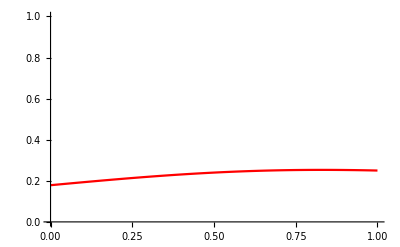

```mathematica
Plot[{.5(rmselfjuvm-rmcompetingjuvm)/.rmcoeff/.rdip/.{l->1,nm->2,nf->2,df->1-dm},
rmownoffspring-rmcompetingoffspring/.rmcoeff/.rdip/.{l->1,nm->2,nf->2,df->1-dm}},
{dm,0,1},PlotStyle->{Blue,Red},PlotRange->{{0,1},{0,1}}]
```

```mathematica
Plot[{.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.rdip/.{l->1,nm->2,nf->2,df->1-dm},
.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->1-dm},
.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->1-dm},
rfownoffspring-rfcompetingoffspring/.rfcoeff/.rdip/.{l->1,nm->2,nf->2,df->1-dm},
rfownoffspring-rfcompetingoffspring/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->1-dm},
rfownoffspring-rfcompetingoffspring/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->1-dm}
},
{dm,0,1},PlotStyle->{{Red,Dotted},{Red,Dashed},{Red},{Blue,Dotted},{Blue,Dashed},{Blue}},PlotRange->{{0,1},{0.4,.55}}]
```

-Graphics-

```mathematica
Plot[{.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->dm},
.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->dm},
rfownoffspring-rfcompetingoffspring/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->dm},
rfownoffspring-rfcompetingoffspring/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->dm}
},
{dm,0,1},PlotStyle->{{Red},{Red,Dotted},{Blue},{Blue,Dotted}},PlotRange->{{0,1},{0,.55}}]
```

-Graphics-

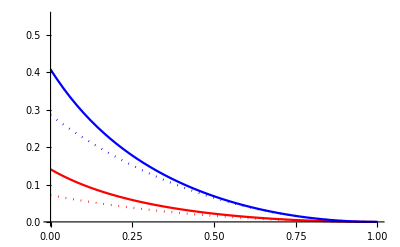

```mathematica
Plot[{.5rfcompetingjuvf/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->dm},
.5 rfcompetingjuvf/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->dm},
rfcompetingoffspring/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->dm},
rfcompetingoffspring/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->dm}
},
{dm,0,1},PlotStyle->{{Red},{Red,Dotted},{Blue},{Blue,Dotted}},PlotRange->{{0,1},{0,.55}}]
```

## Results diplodiploidy

```mathematica
ans[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[selgrada/.rdip/.vdip/.cdip/.tdip/.{f->ϕ,s->σ,g->ϕ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{a,1.5}]
```

```mathematica
ansMI[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[selgrada/.rdipMI/.vdip/.cdip/.tdip/.{f->ϕ,s->σ,g->ϕ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{a,1.5}]
```

```mathematica
ansPI[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[selgrada/.rdipPI/.vdip/.cdip/.tdip/.{f->ϕ,s->σ,g->ϕ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{a,1.5}]
```

```mathematica
ansM[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[selgrada/.rdipM/.vdip/.cdip/.tdip/.{f->ϕ,s->σ,g->ϕ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{a,1.5}]
```

```mathematica
ansP[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[selgrada/.rdipP/.vdip/.cdip/.tdip/.{f->ϕ,s->σ,g->ϕ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{a,1.5}]
```

```mathematica
ansPI[{2,2},{0.5,0.9,1},{1,1/3}]
```

{a→2.23587}

### Figure 1

```mathematica
kk=1/3
```

1/3

```mathematica
μx=1
```

1

```mathematica
ll=1.0
```

1.

```mathematica
a1=Table[{dm,a}/.ans[{2,2},{1-dm,dm,ll},{μx,kk}],{dm,0.01,1,0.01}];
a2=Table[{dm,a}/.ansM[{2,2},{1-dm,dm,ll},{μx,kk}],{dm,0.01,1,0.01}];
a3=Table[{dm,a}/.ansP[{2,2},{1-dm,dm,ll},{μx,kk}],{dm,0.01,1,0.01}];
a4=Table[{dm,a}/.ansMI[{2,2},{1-dm,dm,ll},{μx,kk}],{dm,0.01,1,0.01}];
a5=Table[{dm,a}/.ansPI[{2,2},{1-dm,dm,ll},{μx,kk}],{dm,0.01,1,0.01}];
```

```mathematica
a1
```

{{0.01,1.94744},{0.02,1.95725},{0.03,1.96693},{0.04,1.97648},{0.05,1.98591},{0.06,1.9952},{0.07,2.00435},{0.08,2.01337},{0.09,2.02226},{0.1,2.031},{0.11,2.0396},{0.12,2.04807},{0.13,2.05639},{0.14,2.06456},{0.15,2.07259},{0.16,2.08048},{0.17,2.08821},{0.18,2.09579},{0.19,2.10322},{0.2,2.1105},{0.21,2.11762},{0.22,2.12459},{0.23,2.1314},{0.24,2.13804},{0.25,2.14453},{0.26,2.15086},{0.27,2.15702},{0.28,2.16301},{0.29,2.16884},{0.3,2.1745},{0.31,2.17999},{0.32,2.18531},{0.33,2.19045},{0.34,2.19542},{0.35,2.20022},{0.36,2.20484},{0.37,2.20927},{0.38,2.21353},{0.39,2.21761},{0.4,2.2215},{0.41,2.22521},{0.42,2.22873},{0.43,2.23206},{0.44,2.2352},{0.45,2.23816},{0.46,2.24092},{0.47,2.24348},{0.48,2.24585},{0.49,2.24803},{0.5,2.25},{0.51,2.25177},{0.52,2.25335},{0.53,2.25472},{0.54,2.25588},{0.55,2.25684},{0.56,2.2576},{0.57,2.25814},{0.58,2.25847},{0.59,2.25859},{0.6,2.2585},{0.61,2.25819},{0.62,2.25767},{0.63,2.25693},{0.64,2.25596},{0.65,2.25478},{0.66,2.25338},{0.67,2.25175},{0.68,2.24989},{0.69,2.24781},{0.7,2.2455},{0.71,2.24296},{0.72,2.24019},{0.73,2.23718},{0.74,2.23394},{0.75,2.23047},{0.76,2.22676},{0.77,2.2228},{0.78,2.21861},{0.79,2.21418},{0.8,2.2095},{0.81,2.20458},{0.82,2.19941},{0.83,2.19399},{0.84,2.18832},{0.85,2.18241},{0.86,2.17624},{0.87,2.16981},{0.88,2.16313},{0.89,2.1562},{0.9,2.149},{0.91,2.14154},{0.92,2.13383},{0.93,2.12585},{0.94,2.1176},{0.95,2.10909},{0.96,2.10032},{0.97,2.09127},{0.98,2.08195},{0.99,2.07236},{1.,2.0625}}

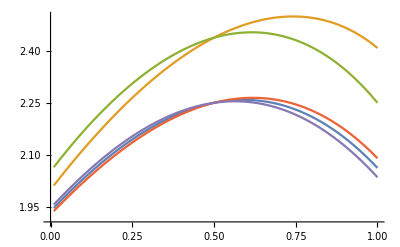

```mathematica
ListLinePlot[{a1,a2,a3,a4,a5}]
```

## Results haplodiploidy

```mathematica
anshap[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[selgrada/.rhapdip/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ,g->ϕ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{a,1.5}]
```

```mathematica
anshapM[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[selgrada/.rhapdipM/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ,g->ϕ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{a,1.5}]
```

```mathematica
anshapP[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[selgrada/.rhapdipP/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ,g->ϕ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{a,1.5}]
```

```mathematica
anshapMI[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[selgrada/.rhapdipMI/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ,g->ϕ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{a,1.5}]
```

```mathematica
anshapPI[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[selgrada/.rhapdipPI/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ,g->ϕ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{a,1.5}]
```

```mathematica
ans[{4,4},{0.9,0.1,0.5},{1,1/3}]
```

{a→2.8916}

### Figure S1

```mathematica
a1hap=Table[{dm,a}/.anshap[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
a2hap=Table[{dm,a}/.anshapM[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
a3hap=Table[{dm,a}/.anshapP[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
a4hap=Table[{dm,a}/.anshapMI[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
a5hap=Table[{dm,a}/.anshapPI[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
```

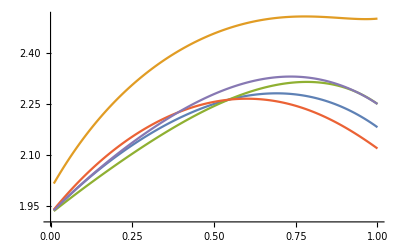

```mathematica
ListLinePlot[{a1hap,a2hap,a3hap,a4hap,a5hap}]
```

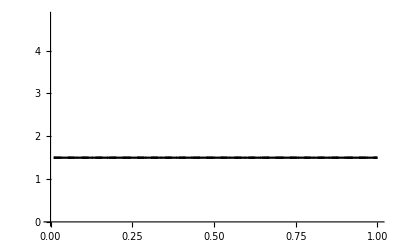

```mathematica
plotbattle1m=ListLinePlot[{Transpose[a1hap][[2]],Transpose[a2hap][[2]],Transpose[a3hap][[2]]},PlotStyle->{{Black,Normal},{Black,Dashed},{Black,Dotted}},PlotRange->{{0,1},{0,4.8}},BaseStyle->{FontFamily->"Helvetica"}]
```

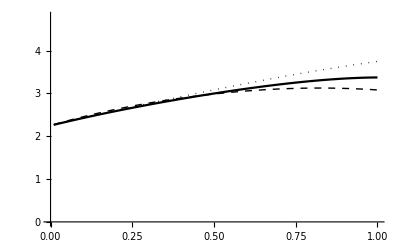

```mathematica
plotbattle2=ListLinePlot[{Transpose[a1hap][[1]],Transpose[a4hap][[1]],Transpose[a5hap][[1]]},PlotStyle->{{Black,Normal},{Black,Dashed,Thick},{Black,Dotted,Thick}},PlotRange->{{0,1},{0,4.8}},BaseStyle->{FontFamily->"Helvetica"}]
```

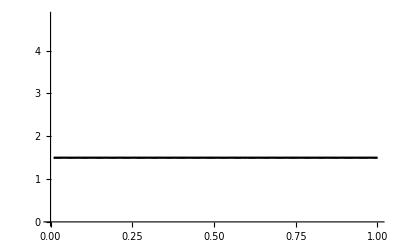

```mathematica
plotbattle2m=ListLinePlot[{Transpose[a1hap][[2]],Transpose[a4hap][[2]],Transpose[a5hap][[2]]},PlotStyle->{{Black,Normal},{Black,Dashed,Thick},{Black,Dotted,Thick}},PlotRange->{{0,1},{0,4.8}},BaseStyle->{FontFamily->"Helvetica"}]
```

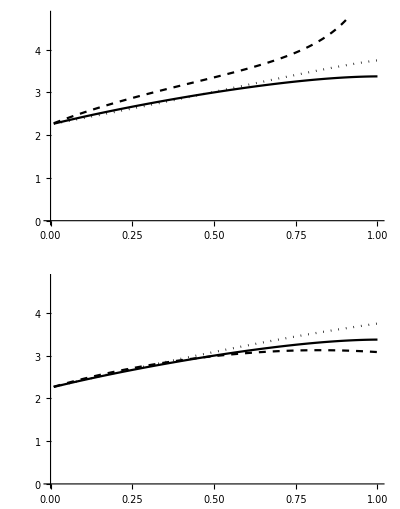
-Graphics-Sex-biased dispersal, d_m=1-d_fFemale age at maturity, a_f

```mathematica
plotaf=Labeled[GraphicsGrid[{{plotbattle1},{plotbattle2}}],{"Sex-biased dispersal, d_m=1-d_f","Female age at maturity, a_f"},{Bottom,Left},RotateLabel->True,LabelStyle->{FontFamily->"Helvetica"}]
```

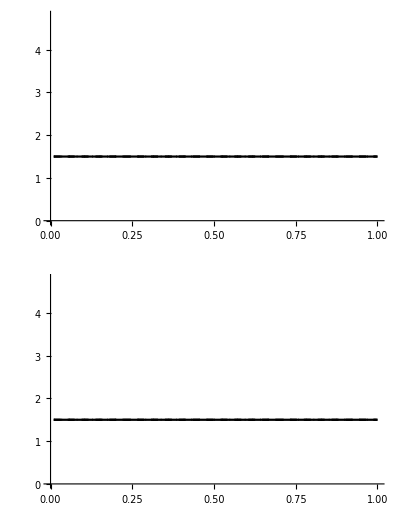
-Graphics-Sex-biased dispersal, d_m=1-d_fMale age at maturity, a_m

```mathematica
plotam=Labeled[GraphicsGrid[{{plotbattle1m},{plotbattle2m}}],{"Sex-biased dispersal, d_m=1-d_f","Male age at maturity, a_m"},{Bottom,Left},RotateLabel->True,LabelStyle->{FontFamily->"Helvetica"}]
```

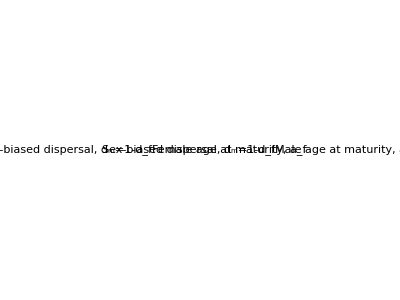

```mathematica
plotafam=GraphicsGrid[{{plotaf,plotam}}]
```

```mathematica
Export[$HomeDirectory<>"/Projects/age_vs_size_imprint/figs/effect_phil/battleground_haplodiploid.pdf",plotafam,ImageSize->{475,250}]
```

/home/bram/Projects/age_vs_size_imprint/figs/effect_phil/battleground_haplodiploid.pdf

## Export to C

```mathematica
rlistdip={{"dip",rdip},{"dipM",rdipM},{"dipP",rdipP},{"dipMI",rdipMI},{"dipPI",rdipPI}};
rlisthapdip={{"hapdip",rhapdip},{"hapdipM",rhapdipM},{"hapdipP",rhapdipP},{"hapdipMI",rhapdipMI},{"hapdipPI",rhapdipPI}};
```

```mathematica
str="";
For[iter=1,iter≤Length[rlistdip],iter++,
str=str<>"af"<>rlistdip[[iter,1]]<>"<-expression("<>ToString[CForm[selgradaf/.rlistdip[[iter,2]]/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}]]<>")\n\n";
str=str<>"am"<>rlistdip[[iter,1]]<>"<-expression("<>ToString[CForm[selgradam/.rlistdip[[iter,2]]/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}]]<>")\n\n";
]
For[iter=1,iter≤Length[rlisthapdip],iter++,
str=str<>"af"<>rlisthapdip[[iter,1]]<>"<-expression("<>ToString[CForm[selgradaf/.rlisthapdip[[iter,2]]/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}]]<>")\n\n";
str=str<>"am"<>rlisthapdip[[iter,1]]<>"<-expression("<>ToString[CForm[selgradam/.rlisthapdip[[iter,2]]/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}]]<>")\n\n";
]
```

```mathematica
Export[$HomeDirectory<>"/Projects/age_vs_size_imprint/figs/effect_phil/mathematica_expressions.txt",str]
```

/home/bram/Projects/age_vs_size_imprint/figs/effect_phil/mathematica_expressions.txt

```mathematica
e
```

e